```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
datax=Import["trot_0.37_allmtax.dat"];
datay=Import["trot_0.37_allmtay.dat"];
datbx=Import["trot_0.37_allmtbx.dat"];
datby=Import["trot_0.37_allmtby.dat"];
```

```mathematica
diffdata=Table[Sqrt[(Total[datax[[i]][[{1,5,9}]]])^2+(Total[datay[[i]][[{1,5,9}]]])^2],{i,1,Length[datax]}];
```

```mathematica
diffdatb=Table[Sqrt[(Total[datbx[[i]][[{1,5,9}]]])^2+(Total[datby[[i]][[{1,5,9}]]])^2],{i,1,Length[datbx]}];
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]]}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]]}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=Min[limval];
maxval=Max[limval];
```

```mathematica
squarelength=7;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
```

```mathematica
slcoordx1=0;
slcoordy1=2;
slcoordx2=-2;
slcoordy2=0;
slcoordx3=0;
slcoordy3=-2;
slcoordx4=2;
slcoordy4=0;
slsquareline=
{Black,Dashed,Thickness[0.015],Line[{{{slcoordx1,slcoordy1},{slcoordx2,slcoordy2}},{{slcoordx2,slcoordy2},{slcoordx3,slcoordy3}},{{slcoordx3,slcoordy3},{slcoordx4,slcoordy4}},{{slcoordx4,slcoordy4},{slcoordx1,slcoordy1}}}]};
```

```mathematica
rmvpoints1=DeleteCases[Table[If[alldiffdata[[i,1]]>coordx3,pt=Null,If[alldiffdata[[i,2]]>coordy3,pt=Null,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]]}]];pt,{i,1,Length[alldiffdata]}],Null];

rmvpoints2=DeleteCases[Table[If[rmvpoints1[[i,1]]<coordx1,pt=Null,If[rmvpoints1[[i,2]]<coordy1,pt=Null,pt={rmvpoints1[[i,1]],rmvpoints1[[i,2]],rmvpoints1[[i,3]]}]];pt,{i,1,Length[rmvpoints1]}],Null];
```

```mathematica
slimval=rmvpoints2[[All,3]];
sminval=Min[slimval];
smaxval=Max[slimval];
spointlegend=BarLegend[{"Rainbow",{sminval,smaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

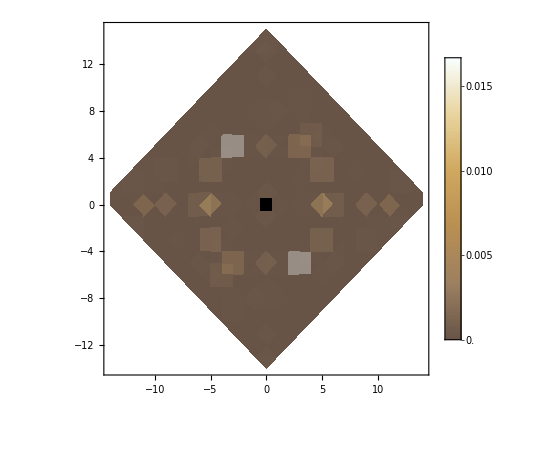

```mathematica
cntlegend=BarLegend[{"CoffeeTones" ,{minval,maxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
cntplot=ListDensityPlot[alldiffdata,PlotRange->All,ColorFunction -> (ColorData["CoffeeTones",(#)^(5) (*(1 - #)^e*)] &),
ImageSize ->450,AspectRatio->1,PlotRange->All,ImagePadding->{{55,92},{55,17}},Epilog -> {Rotate[Text[Style["Site",35],{-18,0}],Pi/2],Text[Style["Site",35],{0, -18.7}]},
FrameLabel->{{"",""},{"",""}},LabelStyle->{FontFamily->"Helvetica",Black,FontSize->20}];

lgcntplot=Legended[cntplot ,Placed[cntlegend,{{0.98,0.77},{-0.1,0.9}}]];

impuritysite=
Graphics[{Black,Rectangle[{-0.5,-0.5},{0.5,0.5}]}];

plwithimp=Show[lgcntplot,impuritysite]
Export["plwithimp.png",plwithimp];
Export["cntlegend.eps",cntlegend];
```